## Jeremy — PS 13 — 2025-03-25

## EIWL3 Sections 33 and 34

```mathematica
Head[ListPlot[{1,2}]]
```

Graphics

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

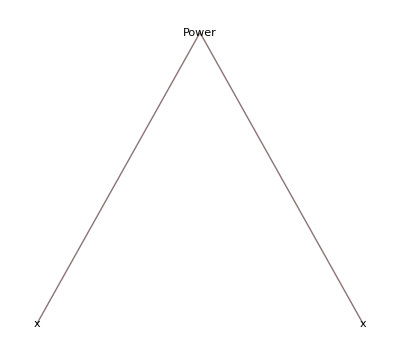
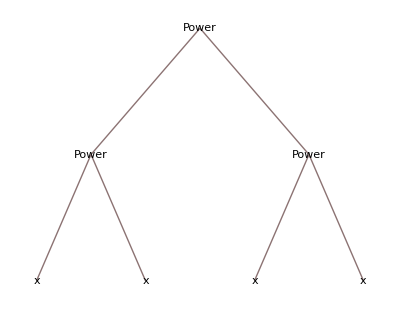
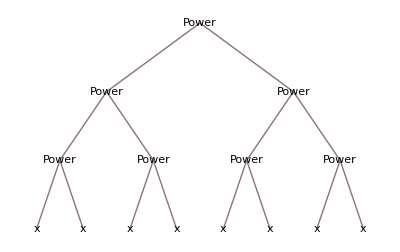
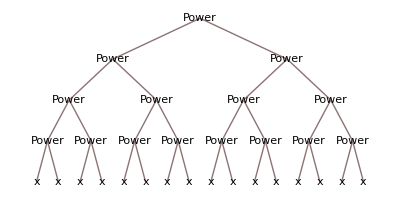
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TreeForm/@NestList[#^#&,x,4]
```

```mathematica
Union[Cases[Flatten[Table[i^2/(j^2+1),{i,20},{j,20}]],_Integer]]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]]
```

-Graphics-

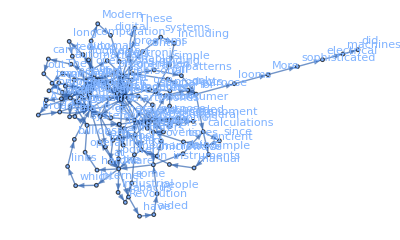

```mathematica
Graph[Rule@@@Partition[Take[TextWords[WikipediaData["computers"]],200],2,1],VertexLabels->All]
```

```mathematica
f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

```mathematica
Values[KeySort[Counts[IntegerDigits[3^100]]]]
```

{7,9,9,5,1,5,4,7,1}

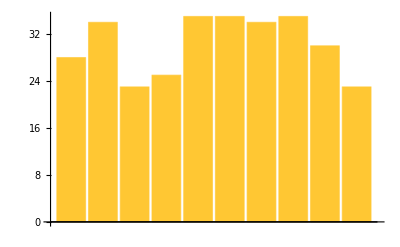

```mathematica
BarChart[KeySort[Counts[IntegerDigits[2^1000]]]]
```

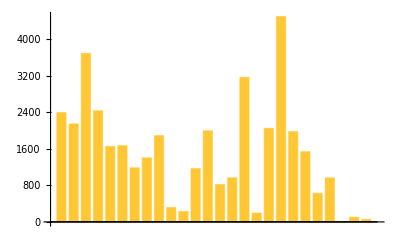

```mathematica
BarChart[Counts[First[ToUpperCase[Characters[#]]]&/@WordList[]]]
```

```mathematica
TakeLargest[Counts[First[Characters[#]]&/@WordList[]],5]
```

<|s→4499,c→3693,p→3168,d→2433,a→2393|>

```mathematica
#q/#u&@LetterCounts[WikipediaData["computers"]]//N
```

0.0401274

```mathematica
TakeLargest[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]],5]
```

<|the→573,and→319,a→269,to→248,she→203|>